### N_ss vs n_tot in SRLG+depletion

```mathematica
Nm=12;
μ0=-2.4;
ϵ=-1;
```

```mathematica
A[ϕ_]:= 2ϕ-1;
B[J_]:= Exp[-J];
```

```mathematica
μ[ϕ_,J_]:=2 Log[A[ϕ] √B[J]+√(1 + A[ϕ]^2(B[J]-1))]-Log[1-A[ϕ]^2]-J;  
μr[ϕ_,nt_]:= μ0 + Log[nt - Nm ϕ + 1];
dμr[ϕ_,nt_]:= -Nm/(nt-Nm ϕ + 1);
```

```mathematica
y[ϕ_,J_,nt_]:= μ[ϕ,J] - μr[ϕ,nt] - dμr[ϕ,nt]ϕ + ϵ;
```

```mathematica
g[nt_]:= ϕ/.FindRoot[y[ϕ,0,nt]==0,{ϕ,0.7}];
```

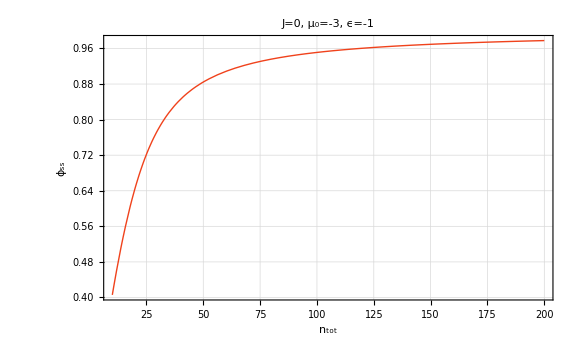

```mathematica
Plot[g[nt],{nt,10,200}, PlotRange->Full,ImageSize->Large, Frame->True,GridLines->Automatic, PlotLabel->"J=0, μ_0=-3, ϵ=-1", LabelStyle->{12,GrayLevel[0]},FrameLabel->{"n_tot","ϕ_ss"},PlotStyle->{Thick,RGBColor[0.94,0.26,0.11]}]
```

### N_ss vs n_tot in Langmuir+depletion

```mathematica
kD[nt_,ϕ_]:= Exp[ϵ+μr[ϕ,nt]]
```

```mathematica
Δ[nt_,ϕ_]:= (kD[nt,ϕ]+1+Nm/nt)^2-4Nm/nt;
ϕe[nt_,ϕ_]:= (kD[nt,ϕ]+1+Nm/nt-√Δ[nt,ϕ])/(2 Nm/nt);
gL[nt_]:= ϕ/.FindRoot[y[ϕ,0,nt]==0,{ϕ,0.7}];
```

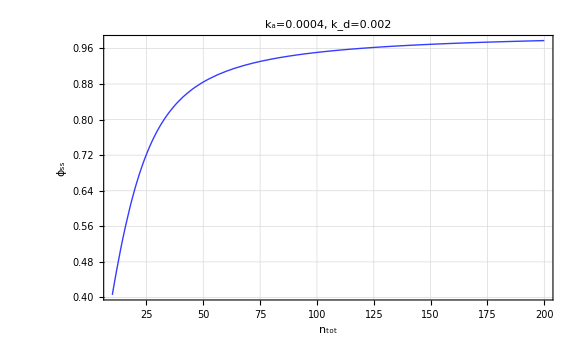

```mathematica
Plot[gL[nt],{nt,10,200},PlotRange->Full,ImageSize->Large, Frame->True,GridLines->Automatic, PlotLabel->"k_a=0.0004, k_d=0.002", LabelStyle->{12,GrayLevel[0]},FrameLabel->{"n_tot","ϕ_ss"},PlotStyle->{Thick,RGBColor[0.21,0.24,1]}]
```

### Comparison between both

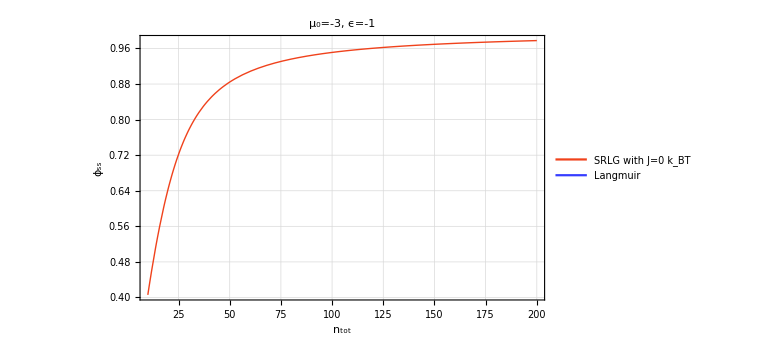

```mathematica
Plot[{g[nt],ϕe[nt]},{nt,10,200},PlotRange->Full,ImageSize->Large, Frame->True,GridLines->Automatic,LabelStyle->{12,GrayLevel[0]},FrameLabel->{"n_tot","ϕ_ss"},PlotStyle->{{Thick,RGBColor[0.94,0.26,0.11]},{Thick,RGBColor[0.21,0.24,1]}},PlotLabel->"μ_0=-3, ϵ=-1",PlotLegends->Placed[LineLegend[{"SRLG with J=0 k_BT","Langmuir"},LegendFunction->Frame],{{0.8,0.2},{0.65,0.7}}]]
```